```mathematica
loadTable[path_]:= Import[NotebookDirectory[]<>path, "Table"]
raw = loadTable["/outputs/5VM_real.p1.4000.out"];
TableForm[raw]
totalColumn[raw_, colNum_]:= Total[Transpose[Drop[raw, 1]][[colNum]]]
allTotalColumns[rawList_, colNum_]:= Function[x, totalColumn[x, colNum]]/@ rawList
plotRunTimes[rawList_, varList_]:=(
searchTime = Transpose[{varList, allTotalColumns[rawList, 2]}];
totalRuntime = Transpose[{varList, allTotalColumns[rawList, 8]}];
referenceFunc = Transpose[{varList, Function[x, 60*x^2.4+500000000] /@varList}];
ListLogPlot[{searchTime, totalRuntime,referenceFunc},  PlotRange->Full, Joined->True, Filling-> Bottom, InterpolationOrder->1, PlotLegends->{"Total Search Step Time", "Total Run time", "60 * (coverage)^2.4 + 5*10^8"}]
)
```

search_blocks | seach_nanos | veri=true_nanos | veri=false_nanos | sol=true_count | sol=false_count | (veri=true_nano_ratio) | (total_nanos) | (search_nanos_ratio) | (sol=true_count_ratio)
2 | 1084732870 | 367008279 | 30366527 | 12331 | 1787 | 0.923582 | 1451741151 | 0.747194 | 0.873424
3 | 2763604389 | 1236983715 | 142729933 | 43088 | 8771 | 0.896551 | 4000588107 | 0.6908 | 0.830868
4 | 4771428604 | 2046931846 | 288156274 | 71191 | 17717 | 0.876597 | 6818360454 | 0.699791 | 0.800727
5 | 6050259273 | 2136498014 | 270982659 | 74315 | 16630 | 0.887441 | 8186757292 | 0.73903 | 0.817142
6 | 3898432985 | 1203469169 | 154372396 | 41352 | 9569 | 0.88631 | 5101902160 | 0.764114 | 0.812081

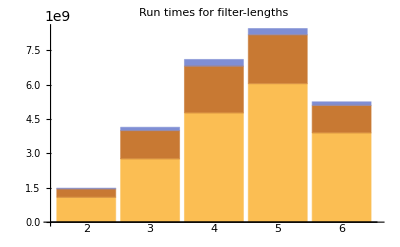

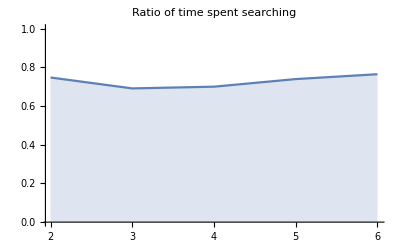

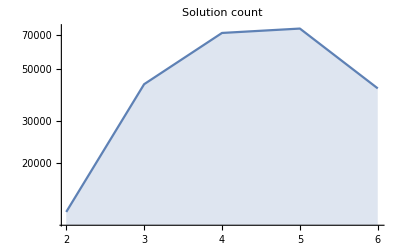

plotRunTimes[]

```mathematica
dropped = Drop[raw, 1];
trans = Transpose[dropped];
cols = trans[[2;;4]];
ready = Transpose[cols];


BarChart[ready, ChartLayout->"Stacked", ChartLabels->{Placed[trans[[1]],Axis],None}, PlotLabel->"Run times for filter-lengths"]

ListLinePlot[trans[[9]],Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotRange->{0,1}, PlotLabel->"Ratio of time spent searching"]
ListLogPlot[trans[[5]],Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotLabel->"Solution count", Joined->True]


plotRunTimes[]
```

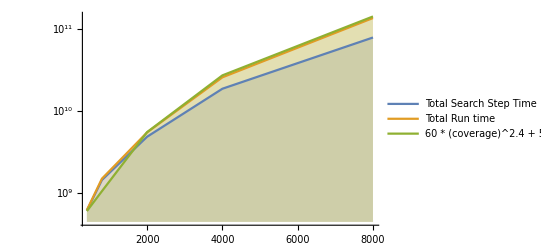

```mathematica
raws = loadTable/@ {"/outputs/5VM_real.p1.400.out", "/outputs/5VM_real.p1.800.out", "/outputs/5VM_real.p1.2000.out", "/outputs/5VM_real.p1.4000.out", "/outputs/5VM_real.p1.8000.out"};
varList = {400, 800, 2000, 4000, 8000};
plotRunTimes[raws, varList]
```